```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
DelEle[list_,element_]:=Delete[list,FirstPosition[list,element]](* Delete Element *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}]
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
RestMaxCurrEdgeNum[PartLoop_]:=(
For[i=1,
(Length[Complement[VertexList[{Ruleg[[SortCurr[[i]]]]}],VertexList[PartLoop]]]== 0|| Intersection[VertexList[PartLoop],VertexList[{Ruleg[[SortCurr[[i]]]]}]]== {}),
i++,];
SortCurr[[i]]
)
```

```mathematica
RestMaxCurrEdge[PartLoop_]:=Ruleg[[RestMaxCurrEdgeNum[PartLoop]]]
```

```mathematica
RestMaxCurrEdgeList[PartLoop_]:=VertexList[{RestMaxCurrEdge[PartLoop]}]
```

```mathematica
RestMaxCurrEdgeLoopSide[PartLoop_]:=Intersection[VertexList[PartLoop],RestMaxCurrEdgeList[PartLoop]][[1]]
```

```mathematica
RestMaxCurrEdgeRestSide[PartLoop_]:=DelEle[RestMaxCurrEdgeList[PartLoop],RestMaxCurrEdgeLoopSide[PartLoop]][[1]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,RestMaxCurrEdgeRestSide[PartLoop]]]]
```

```mathematica
InsertEdge[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]->RestMaxCurrEdgeRestSide[PartLoop],RestMaxCurrEdgeRestSide[PartLoop]->VertexList[{LoopDelEdge[PartLoop]}][[2]]}]]
```

### 自動表示

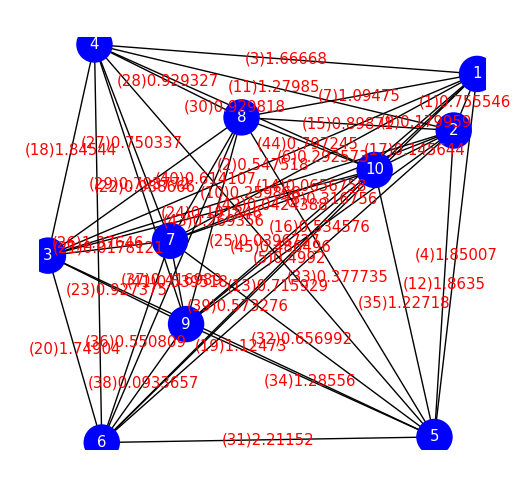

{33.8083,{1,8,4,7,3,6,9,5,10,2}}

{32.7656,{1,10,8,4,3,7,9,6,5,2,1}}

3

```mathematica
TourCost=0;
MathematicaSolution={0,{}};
For[RpeatCount=1,TourCost== MathematicaSolution[[1]],RpeatCount++,
Pin=Table[{RandomReal[10],RandomReal[10]},{i,10}];(*Point input*)
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(*Ggraph input*)
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
SortCurr=Reverse[Ordering[Abs[Curr]]];
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
MaxPartLoop={};
For[i=3,Length[MaxPartLoop]==0,i++,
MaxPartLoop=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[i]]]]]],
Infinity,All];
];
MaxPartLoop=EdgeRules[MaxPartLoop[[1]]];
Clear[InsertPartLoop];
InsertPartLoop={MaxPartLoop};
For[j=1,Complement[VertexList[Gin],VertexList[InsertPartLoop[[j]]]]≠{},j++,
InsertPartLoop=Append[InsertPartLoop,InsertEdge[InsertPartLoop[[j]]]]
];
EdgeSolution=Last[InsertPartLoop];

TourCost=Total[EdgeDList[EdgeSolution]];
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]->_][[1]],2]]]
];
MathematicaSolution=FindShortestTour[Pin];
]
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
{TourCost,VertexSolution}
MathematicaSolution
RpeatCount
```

```mathematica
InsertPartLoop
```

{{1→10,10→2,2→7,7→1},{10→2,2→7,7→1,1→5,5→10},{10→2,2→7,1→5,5→10,7→3,3→1},{10→2,2→7,1→5,5→10,3→1,7→4,4→3},{10→2,1→5,5→10,3→1,7→4,4→3,2→8,8→7},{10→2,1→5,5→10,3→1,7→4,4→3,2→8,8→6,6→7},{10→2,1→5,5→10,3→1,7→4,4→3,2→8,8→6,6→9,9→7}}

```mathematica
SortCurr
```

{4,17,12,9,14,6,35,2,3,11,21,18,19,44,40,24,28,33,39,41,29,32,45,25,16,23,43,31,1,36,8,26,15,34,10,22,38,37,27,7,5,13,30,42,20}

```mathematica
Total[EdgeDList[{4->9,9->6,6->10}]]
```

7.79288

```mathematica
Total[EdgeDList[{4->6,6->9,9->10}]]
```

9.47263

```mathematica
TriTourDiff[9->10,6]
```

0.00373973

```mathematica
TriTourDiff[4->9,6]
```

1.68349